# Local Tidal Tensor via ZAMO

## A Unified Approach for Axisymmetric Spacetimes

```mathematica
ClearAll["`*"](* reset ALL variables of this notebook context *)
```

## 0. Define Helper Functions

### Code for optimising symbolic expressions to C++

ref. https://github.com/ABHModels/raytransfer

```mathematica
(*::Package::*)

BeginPackage["OptimizeExpressionToC`"];

OptimizeExpressionToC::usage="Generates optimized version of expression in C";

ExtractTags::usage="";
ClearTagText::usage="";
TagExistQ::usage="";
AppendToTag::usage="";

Begin["Private`"];

OptimizeExpressionToC[expr_List]:=Module[{optimizedExpr,mainExpr,n,m,defs,output},optimizedExpr=Experimental`OptimizeExpression[expr];If[ToString@optimizedExpr[[1,0]]=="Block",{n=Length[optimizedExpr[[1,1]]];mainExpr=optimizedExpr[[1,2,n+1]];},{n=0;mainExpr=Flatten@{optimizedExpr[[1]]};}];m=Length[mainExpr];defs=Table["double "<>ToString@CForm@optimizedExpr[[1,2,i,1]]<>" = "<>ToString@CForm@optimizedExpr[[1,2,i,2]]<>";",{i,1,n}];output=MapIndexed["out("<>StringJoin@Riffle[ToString/@(#2-1),""]<>") = "<>ToString@CForm@#1<>";"&,mainExpr,{ArrayDepth[mainExpr]}];StringReplace[Join[defs,output],"Compile_$"->"t"]];

End[];
Null

ExtractTags[string_String]:=Module[{regex,extractTag},regex=RegularExpression["\\n([^\\n]*)// (\\[|</?)([^\\]\\n]*)(\\]|>)[^\\n]*\\n"];extractTag[bounds_]:=Module[{substring,indentation,tagType,tag},substring=StringTake[string,bounds];{{indentation,tagType,tag}}=StringCases[substring,regex->{"$1","$2","$3"}];Association["indentation"->indentation,"tagType"->tagType,"tag"->tag,"start"->bounds[[1]]+1,"end"->bounds[[2]]]];extractTag[#]&/@StringPosition[string,regex]];

TagExistQ[string_String,tag_String]:=AnyTrue[ExtractTags[string],#[["tag"]]==tag&];

ClearTagText[string_String,tag_String]:=Module[{tags,startTag,endTag,x},tags=ExtractTags[string];startTag=FirstCase[tags,x_/;x[["tag"]]==tag&&x[["tagType"]]=="<"];endTag=FirstCase[tags,x_/;x[["tag"]]==tag&&x[["tagType"]]=="</"];StringTake[string,{1,startTag[["end"]]}]<>StringTake[string,{endTag[["start"]],StringLength[string]}]]

AppendToTag[string_String,tag_String,linesToAppend_List]:=Module[{tags,startTag,indent,x},tags=ExtractTags[string];startTag=FirstCase[tags,x_/;x[["tag"]]==tag&&x[["tagType"]]=="<"];indent=startTag[["indentation"]];StringTake[string,{1,startTag[["end"]]}]<>StringRiffle[linesToAppend,{indent,"\n"<>indent,"\n"}]<>StringTake[string,{startTag[["end"]]+1,StringLength[string]}]];

AppendToTag[string_String,tag_String,stringToAppend_String]:=AppendToTag[string,tag,StringSplit[stringToAppend,"\n"]];
Null

EndPackage[];
```

```mathematica
outputMetric[matrix_,filename_:"metric.cpp"]:=Module[{text,meat,header,footer,output},text=OptimizeExpressionToC[{matrix[[1]][[1]],matrix[[1]][[2]],matrix[[1]][[3]],matrix[[1]][[4]],matrix[[2]][[1]],matrix[[2]][[2]],matrix[[2]][[3]],matrix[[2]][[4]],matrix[[3]][[1]],matrix[[3]][[2]],matrix[[3]][[3]],matrix[[3]][[4]],matrix[[4]][[1]],matrix[[4]][[2]],matrix[[4]][[3]],matrix[[4]][[4]]}];
meat=ToString[Column[StringReplace[text,{"Sqrt"->"sqrt","Power(E,"->"exp(","Power"->"pow","Sin"->"sin","Cos"->"cos","Csc"->"1/sin","Cot"->"1/tan","double"->"double",";,"->";\n    ","out(0)"->"g[0][0]","out(1)"->"g[0][1]","out(2)"->"g[0][2]","out(3)"->"g[0][3]","out(4)"->"g[1][0]","out(5)"->"g[1][1]","out(6)"->"g[1][2]","out(7)"->"g[1][3]","out(8)"->"g[2][0]","out(9)"->"g[2][1]","out(10)"->"g[2][2]","out(11)"->"g[2][3]","out(12)"->"g[3][0]","out(13)"->"g[3][1]","out(14)"->"g[3][2]","out(15)"->"g[3][3]"}]]];
header="void metric(double r, double chi, double g[4][4])\n{\n";
footer="\n}";
output=header<>meat<>footer;
Export[filename,output,"Text"]]

outputChristoffel[matrix_,filename_:"christoffel.cpp"]:=Module[{text,meat,header,footer,output},text=OptimizeExpressionToC[{matrix[[1]][[1]][[1]],matrix[[1]][[1]][[2]],matrix[[1]][[1]][[3]],matrix[[1]][[1]][[4]],matrix[[1]][[2]][[1]],matrix[[1]][[2]][[2]],matrix[[1]][[2]][[3]],matrix[[1]][[2]][[4]],matrix[[1]][[3]][[1]],matrix[[1]][[3]][[2]],matrix[[1]][[3]][[3]],matrix[[1]][[3]][[4]],matrix[[1]][[4]][[1]],matrix[[1]][[4]][[2]],matrix[[1]][[4]][[3]],matrix[[1]][[4]][[4]],matrix[[2]][[1]][[1]],matrix[[2]][[1]][[2]],matrix[[2]][[1]][[3]],matrix[[2]][[1]][[4]],matrix[[2]][[2]][[1]],matrix[[2]][[2]][[2]],matrix[[2]][[2]][[3]],matrix[[2]][[2]][[4]],matrix[[2]][[3]][[1]],matrix[[2]][[3]][[2]],matrix[[2]][[3]][[3]],matrix[[2]][[3]][[4]],matrix[[2]][[4]][[1]],matrix[[2]][[4]][[2]],matrix[[2]][[4]][[3]],matrix[[2]][[4]][[4]],matrix[[3]][[1]][[1]],matrix[[3]][[1]][[2]],matrix[[3]][[1]][[3]],matrix[[3]][[1]][[4]],matrix[[3]][[2]][[1]],matrix[[3]][[2]][[2]],matrix[[3]][[2]][[3]],matrix[[3]][[2]][[4]],matrix[[3]][[3]][[1]],matrix[[3]][[3]][[2]],matrix[[3]][[3]][[3]],matrix[[3]][[3]][[4]],matrix[[3]][[4]][[1]],matrix[[3]][[4]][[2]],matrix[[3]][[4]][[3]],matrix[[3]][[4]][[4]],matrix[[4]][[1]][[1]],matrix[[4]][[1]][[2]],matrix[[4]][[1]][[3]],matrix[[4]][[1]][[4]],matrix[[4]][[2]][[1]],matrix[[4]][[2]][[2]],matrix[[4]][[2]][[3]],matrix[[4]][[2]][[4]],matrix[[4]][[3]][[1]],matrix[[4]][[3]][[2]],matrix[[4]][[3]][[3]],matrix[[4]][[3]][[4]],matrix[[4]][[4]][[1]],matrix[[4]][[4]][[2]],matrix[[4]][[4]][[3]],matrix[[4]][[4]][[4]]}];
meat=ToString[Column[StringReplace[text,{"Sqrt"->"sqrt","Power(E,"->"exp(","Power"->"pow","Sin"->"sin","Cos"->"cos","Csc"->"1/sin","Cot"->"1/tan","double"->"double",";,"->";\n    ","out(0)"->"christ[0][0][0]","out(1)"->"christ[0][0][1]","out(2)"->"christ[0][0][2]","out(3)"->"christ[0][0][3]","out(4)"->"christ[0][1][0]","out(5)"->"christ[0][1][1]","out(6)"->"christ[0][1][2]","out(7)"->"christ[0][1][3]","out(8)"->"christ[0][2][0]","out(9)"->"christ[0][2][1]","out(10)"->"christ[0][2][2]","out(11)"->"christ[0][2][3]","out(12)"->"christ[0][3][0]","out(13)"->"christ[0][3][1]","out(14)"->"christ[0][3][2]","out(15)"->"christ[0][3][3]","out(16)"->"christ[1][0][0]","out(17)"->"christ[1][0][1]","out(18)"->"christ[1][0][2]","out(19)"->"christ[1][0][3]","out(20)"->"christ[1][1][0]","out(21)"->"christ[1][1][1]","out(22)"->"christ[1][1][2]","out(23)"->"christ[1][1][3]","out(24)"->"christ[1][2][0]","out(25)"->"christ[1][2][1]","out(26)"->"christ[1][2][2]","out(27)"->"christ[1][2][3]","out(28)"->"christ[1][3][0]","out(29)"->"christ[1][3][1]","out(30)"->"christ[1][3][2]","out(31)"->"christ[1][3][3]","out(32)"->"christ[2][0][0]","out(33)"->"christ[2][0][1]","out(34)"->"christ[2][0][2]","out(35)"->"christ[2][0][3]","out(36)"->"christ[2][1][0]","out(37)"->"christ[2][1][1]","out(38)"->"christ[2][1][2]","out(39)"->"christ[2][1][3]","out(40)"->"christ[2][2][0]","out(41)"->"christ[2][2][1]","out(42)"->"christ[2][2][2]","out(43)"->"christ[2][2][3]","out(44)"->"christ[2][3][0]","out(45)"->"christ[2][3][1]","out(46)"->"christ[2][3][2]","out(47)"->"christ[2][3][3]","out(48)"->"christ[3][0][0]","out(49)"->"christ[3][0][1]","out(50)"->"christ[3][0][2]","out(51)"->"christ[3][0][3]","out(52)"->"christ[3][1][0]","out(53)"->"christ[3][1][1]","out(54)"->"christ[3][1][2]","out(55)"->"christ[3][1][3]","out(56)"->"christ[3][2][0]","out(57)"->"christ[3][2][1]","out(58)"->"christ[3][2][2]","out(59)"->"christ[3][2][3]","out(60)"->"christ[3][3][0]","out(61)"->"christ[3][3][1]","out(62)"->"christ[3][3][2]","out(63)"->"christ[3][3][3]"}]]];
header="void christoffel(double r, double chi, double christ[4][4][4])\n{\n";
footer="\n}";
output=header<>meat<>footer;
Export[filename,output,"Text"]]

outputTidal[matrix_,filename_:"Cloc.cpp"]:=Module[{text,meat,header,footer,output},text=OptimizeExpressionToC[{matrix[[1]][[1]],matrix[[1]][[2]],matrix[[1]][[3]],matrix[[1]][[4]],matrix[[2]][[1]],matrix[[2]][[2]],matrix[[2]][[3]],matrix[[2]][[4]],matrix[[3]][[1]],matrix[[3]][[2]],matrix[[3]][[3]],matrix[[3]][[4]],matrix[[4]][[1]],matrix[[4]][[2]],matrix[[4]][[3]],matrix[[4]][[4]]}];
meat=ToString[Column[StringReplace[text,{"Sqrt"->"sqrt","Power(E,"->"exp(","Power"->"pow","Abs"->"abs","Sin"->"sin","Cos"->"cos","Csc"->"1/sin","Cot"->"1/tan",";,"->";\n    ","double"->"complex<double>","out(0)"->"C[0][0]","out(1)"->"C[0][1]","out(2)"->"C[0][2]","out(3)"->"C[0][3]","out(4)"->"C[1][0]","out(5)"->"C[1][1]","out(6)"->"C[1][2]","out(7)"->"C[1][3]","out(8)"->"C[2][0]","out(9)"->"C[2][1]","out(10)"->"C[2][2]","out(11)"->"C[2][3]","out(12)"->"C[3][0]","out(13)"->"C[3][1]","out(14)"->"C[3][2]","out(15)"->"C[3][3]"}]]];
header="void ClocH(complex<double> M, complex<double> a, complex<double> Q, complex<double> e, complex<double> lz, complex<double> ep, complex<double> q, complex<double> r, complex<double> theta, complex<double> dt, complex<double> dr, complex<double> dtheta, complex<double> dphi, complex<double> C[4][4])\n{\n";
footer="\n}";
output=header<>meat<>footer;
Export[filename,output,"Text"]]
```

### Functions for solving IBSO radii

```mathematica
Ralt[r_,ep_,lz_,a_,Q_,e_,m_,Lambda_]=(ep*(r^2+a^2)-a*lz-e*Q*r)^2-(r^2-2*r+a^2+Q^2)*(m^2*r^2+(a*ep-lz)^2+lz^2*(Lambda^2)/(1-Lambda^2));

dRaltdr[r_,ep_,lz_,a_,Q_,e_,m_,Lambda_]=D[Ralt[r,ep,lz,a,Q,e,m,Lambda],r];

dRaltdr2[r_,ep_,lz_,a_,Q_,e_,m_,Lambda_]=D[dRaltdr[r,ep,lz,a,Q,e,m,Lambda],r];

solplus[var1_,var2_,var3_]:=Module[{spin=var1,charge=var2,lam=var3,out},out=NSolve[Ralt[rsol,1,lzsol,var1,var2,0,1,var3]==0&&dRaltdr[rsol,1,lzsol,var1,var2,0,1,var3]==0&&rsol>0&&lzsol>0,{rsol,lzsol},Reals,WorkingPrecision->16]/. {{}->{rsol->0,lzsol->0}};
out];

solminus[var1_,var2_,var3_]:=Module[{spin=var1,charge=var2,lam=var3,out},out=NSolve[Ralt[rsol,1,lzsol,var1,var2,0,1,var3]==0&&dRaltdr[rsol,1,lzsol,var1,var2,0,1,var3]==0&&rsol>0&&lzsol<0,{rsol,lzsol},Reals,WorkingPrecision->16]/. {{}->{rsol->0,lzsol->0}};
out];

momentum[r_,a_,Q_]=(-a^2+r*(r-Q^2)-(r^2-2*r+a^2+Q^2)*Sqrt[r])/(a*(r-1));

carterk[r_,a_,Q_]=(r*(a*(-3 + r)*r + a^3*(1 + r) + a*Q^2*(1 + r) + 2*Sqrt[a^2*r*(a^2 + Q^2 + (-2 + r)*r)^2]))/(a*(-1 + r)^2);

carterq[r_,a_,Q_]=carterk[r,a,Q]-(momentum[r,a,Q]-a)^2;
```

```mathematica
Simplify[carterq[r,a,Q]]
```

-1/(a^2 (-1+r)^2)r (2 a^4 √r-2 a √(a^2 r (a^2+Q^2+(-2+r) r)^2)+(1+√r)^2 (Q^2-2 r+r^(3/2))^2+a^2 (Q^2 (1+4 √r+r)+r (-1-6 √r-r+2 r^(3/2))))

### Modules for constructing tensors

```mathematica
getR[a0_,b0_,c0_,d0_]:=Module[{i0=0,j0=0,k0=0,l0=0,component=0},For[i0=1,i0<=4,i0++,For[j0=1,j0<=4,j0++,For[k0=1,k0<=4,k0++,For[l0=1,l0<=4,l0++,component+=Part[Robs,i0,j0,k0,l0]*Part[matdown,a0,i0]*Part[matdown,b0,j0]*Part[matdown,c0,k0]*Part[matdown,d0,l0];]]]];
component]

getRH[a0_,b0_,c0_,d0_]:=Module[{i0=0,j0=0,k0=0,l0=0,component=0},For[i0=1,i0<=4,i0++,component+=Part[Rlnrf,i0,b0,c0,d0]*Part[eta,a0,i0];];
component]

getRIC[a0_,b0_]:=Module[{i0=0,j0=0,k0=0,l0=0,component=0},For[i0=1,i0<=4,i0++,For[j0=1,j0<=4,j0++,component+=Part[eta,i0,j0]*Part[Rlnrf,i0,a0,j0,b0];]];
component]

getC[a0_,b0_]:=Module[{i0=0,j0=0,k0=0,l0=0,component=0},For[i0=1,i0<=4,i0++,For[j0=1,j0<=4,j0++,component-=Part[Rlnrf,a0,i0,b0,j0]*Part[Ulnrf,i0]*Part[Ulnrf,j0];]];
component]

getCH[a0_,b0_]:=Module[{i0=0,j0=0,k0=0,l0=0,component=0},For[i0=1,i0<=4,i0++,For[j0=1,j0<=4,j0++,component-=Part[RlnrfH,a0,i0,b0,j0]*Part[Ulnrf,i0]*Part[Ulnrf,j0];]];
component]

getCobs[a0_,b0_]:=Module[{i0=0,j0=0,k0=0,l0=0,component=0},For[i0=1,i0<=4,i0++,For[j0=1,j0<=4,j0++,component-=Part[Robs,a0,i0,b0,j0]*Part[U,i0]*Part[U,j0];]];
component]

getCobsH[a0_,b0_]:=Module[{i0=0,j0=0,k0=0,l0=0,component=0},For[i0=1,i0<=4,i0++,For[j0=1,j0<=4,j0++,component-=Part[RobsH,a0,i0,b0,j0]*Part[U,i0]*Part[U,j0];]];
component]

getClocH[mu0_,nu0_]:=Module[{i0=0,j0=0,k0=0,l0=0,component=0},For[i0=1,i0<=4,i0++,For[j0=1,j0<=4,j0++,component+=Part[ClnrfH,i0,j0]*Part[lorentz,mu0,i0]*Part[lorentzinv,j0,nu0];]];
component]

genRlnrf[]:=Module[{i0,j0,k0,l0,output},output=Table[getR[i0,j0,k0,l0],{i0,1,4},{j0,1,4},{k0,1,4},{l0,1,4}];
Simplify[output,Assumptions->assume]]

genRlnrfH[]:=Module[{i0,j0,k0,l0,output},output=Table[getRH[i0,j0,k0,l0],{i0,1,4},{j0,1,4},{k0,1,4},{l0,1,4}];
Simplify[output,Assumptions->assume]]

genRIClnrf[]:=Module[{i0,j0,output},output=Table[getRIC[i0,j0],{i0,1,4},{j0,1,4}];
Simplify[output,Assumptions->assume]]

genUlnrf[]:=Module[{i0,j0,output},output=ConstantArray[0,{4}];
For[i0=1,i0<=4,i0++,For[j0=1,j0<=4,j0++,output[[i0]]+=Part[U,j0]*Part[matup,i0,j0];]];
Simplify[output,Assumptions->assume]]

genClnrf[]:=Module[{i0,j0,output},output=Table[getC[i0,j0],{i0,1,4},{j0,1,4}];
output]

genClnrfH[]:=Module[{i0,j0,output},output=Table[getCH[i0,j0],{i0,1,4},{j0,1,4}];
output]

genCobs[]:=Module[{i0,j0,output},output=Table[getCobs[i0,j0],{i0,1,4},{j0,1,4}];
output]

genCobsH[]:=Module[{i0,j0,output},output=Table[getCobsH[i0,j0],{i0,1,4},{j0,1,4}];
output]

genClocH[]:=Module[{i0,j0,output},output=Table[getClocH[i0,j0],{i0,1,4},{j0,1,4}];
output]

genLorentz[]:=Module[{i0,j0,output,beta,gamma,betar,betatheta,betaphi},beta=Sqrt[Part[UlnrfN,2]^2+Part[UlnrfN,3]^2+Part[UlnrfN,4]^2];
gamma=1/Sqrt[1-beta^2];
betar=Part[UlnrfN,2];
betatheta=Part[UlnrfN,3];
betaphi=Part[UlnrfN,4];
output={{gamma,-gamma*betar,-gamma*betatheta,-gamma*betaphi},{-gamma*betar,1+(gamma-1)*betar^2/(beta^2),(gamma-1)*betar*betatheta/(beta^2),(gamma-1)*betar*betaphi/(beta^2)},{-gamma*betatheta,(gamma-1)*betar*betatheta/(beta^2),1+(gamma-1)*betatheta^2/(beta^2),(gamma-1)*betatheta*betaphi/(beta^2)},{-gamma*betaphi,(gamma-1)*betar*betaphi/(beta^2),(gamma-1)*betatheta*betaphi/(beta^2),1+(gamma-1)*betaphi^2/(beta^2)}};
output]

genLorentzinv[]:=Module[{i0,j0,output,beta,gamma,betar,betatheta,betaphi},beta=Sqrt[Part[UlnrfN,2]^2+Part[UlnrfN,3]^2+Part[UlnrfN,4]^2];
gamma=1/Sqrt[1-beta^2];
betar=Part[UlnrfN,2];
betatheta=Part[UlnrfN,3];
betaphi=Part[UlnrfN,4];
output={{gamma,gamma*betar,gamma*betatheta,gamma*betaphi},{gamma*betar,1+(gamma-1)*betar^2/(beta^2),(gamma-1)*betar*betatheta/(beta^2),(gamma-1)*betar*betaphi/(beta^2)},{gamma*betatheta,(gamma-1)*betar*betatheta/(beta^2),1+(gamma-1)*betatheta^2/(beta^2),(gamma-1)*betatheta*betaphi/(beta^2)},{gamma*betaphi,(gamma-1)*betar*betaphi/(beta^2),(gamma-1)*betatheta*betaphi/(beta^2),1+(gamma-1)*betaphi^2/(beta^2)}};
output]
```

## 1. Construct Metric and LNRF Tetrad

### Define Metric Functions (Teo Wormhole)

```mathematica
Nfunc[r_,theta_]=1+(4*a*Cos[theta])^2/r;

Kfunc[r_,theta_] =1+(4*a*Cos[theta])^2/r;

bfunc[r_,theta_] = 1;

omegafunc[r_,theta_]=2a/r^3;

(*Clear[Nfunc,Kfunc,bfunc,omegafunc];*)

nu = Log[Nfunc[r,theta]];

psi = Log[r*Kfunc[r,theta]*Sin[theta]];

mu1 = Log[1/(1-bfunc[r,theta]/r)] / 2;

mu2 = Log[r*Kfunc[r,theta]];

omega = omegafunc[r,theta];

(* Assumptions help to improve results from Simplify and FullSimplify *)
assume = {0 < a , M >0,0 < theta < Pi/2,ep>0,r>2,lz>0};
```

### Construct metric

```mathematica
g00 = -Exp[2 * nu] + omega^2 * Exp[2 * psi];

g11 = Exp[2 * mu1];

g22 = Exp[2 * mu2];

g33 = Exp[2 * psi];

g03 = -omega * Exp[2 * psi];

g30 = g03;

G = Simplify[{{g00, 0, 0, g03}, {0, g11, 0, 0}, {0, 0, g22, 0}, {g03,
     0, 0, g33}}];

G // MatrixForm
eta = {{-1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}};
Ginv = Simplify[Inverse[G],Assumptions->assume];
Ginv // MatrixForm
eta//MatrixForm
```

(-((r+16 a^2 Cos[theta]^2)^2 (r^4-4 a^2 Sin[theta]^2))/r^6 | 0 | 0 | -(2 a (r+16 a^2 Cos[theta]^2)^2 Sin[theta]^2)/r^3
0 | r/(-1+r) | 0 | 0
0 | 0 | (r+16 a^2 Cos[theta]^2)^2 | 0
-(2 a (r+16 a^2 Cos[theta]^2)^2 Sin[theta]^2)/r^3 | 0 | 0 | (r+16 a^2 Cos[theta]^2)^2 Sin[theta]^2)

(-r^2/((r+16 a^2 Cos[theta]^2)^2) | 0 | 0 | -(2 a)/(r (r+16 a^2 Cos[theta]^2)^2)
0 | (-1+r)/r | 0 | 0
0 | 0 | 1/((r+16 a^2 Cos[theta]^2)^2) | 0
-(2 a)/(r (r+16 a^2 Cos[theta]^2)^2) | 0 | 0 | (-4 a^2+r^4 Csc[theta]^2)/(r^4 (r+16 a^2 Cos[theta]^2)^2))

(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

First  integrals  to  geodesic  equations, assuming  theta = Pi/2

```mathematica
Dfunc=Nfunc[r,theta]*Kfunc[r,theta]*r*Sin[theta];
dsub = {
dt -> (Part[G,4,4]*ep+Part[G,1,4]*lz)/(Dfunc^2),
dr -> -Sqrt[Part[Ginv,2,2]*((Part[G,4,4]*ep^2+2*Part[G,1,4]*lz*ep+Part[G,1,1]*lz^2)/(Dfunc^2)-1)], 
dtheta ->0, 
dphi ->-(Part[G,1,4]*ep+Part[G,1,1]*lz)/(Dfunc^2)
};
dsub=Simplify[dsub];
dsubalt=dsub/.{lz->0}
```

{dt→(ep r^2)/((r+16 a^2 Cos[theta]^2)^2),dr→-√(((-1+r) (-r^6+ep^2 r^6-32 a^2 r^5 Cos[theta]^2-256 a^4 r^4 Cos[theta]^4))/(r^5 (r+16 a^2 Cos[theta]^2)^2)),dtheta→0,dphi→(2 a ep)/(r (r+16 a^2 Cos[theta]^2)^2)}

### Construct LNRF tetrad

```mathematica
etup = {Exp[nu], 0, 0, 0};

erup = {0, Exp[mu1], 0, 0};

ethetaup = {0, 0, Exp[mu2], 0};

ephiup = {-omega * Exp[psi], 0, 0, Exp[psi]};

etdown = {Exp[-nu], 0, 0, omega * Exp[-nu]};

erdown = {0, Exp[-mu1], 0, 0};

ethetadown = {0, 0, Exp[-mu2], 0};

ephidown = {0, 0, 0, Exp[-psi]};

matup = Simplify[{etup, erup, ethetaup, ephiup}, Assumptions -> assume
    ];

matdown = Simplify[{etdown, erdown, ethetadown, ephidown}, Assumptions
     -> assume];

matup //MatrixForm
matdown //MatrixForm
```

(1+(16 a^2 Cos[theta]^2)/r | 0 | 0 | 0
0 | √(r/(-1+r)) | 0 | 0
0 | 0 | r+16 a^2 Cos[theta]^2 | 0
-(2 a (r+16 a^2 Cos[theta]^2) Sin[theta])/r^3 | 0 | 0 | (r+16 a^2 Cos[theta]^2) Sin[theta])

(r/(r+16 a^2 Cos[theta]^2) | 0 | 0 | (2 a)/(r^2 (r+16 a^2 Cos[theta]^2))
0 | √((-1+r)/r) | 0 | 0
0 | 0 | 1/(r+16 a^2 Cos[theta]^2) | 0
0 | 0 | 0 | Csc[theta]/(r+16 a^2 Cos[theta]^2))

## 2. Compute Riemann Tensors in LNRF

### Riemann tensor in observer frame

last two lines take quite a while (~5 min)

```mathematica
metric = ResourceFunction["MetricTensor"][G, {t, r, theta, phi}, True,
     True];

riemann = ResourceFunction["RiemannTensor"][metric];

riemann2 = riemann["CovariantRiemannTensor"];

AbsoluteTiming[
Robs = riemann2["ReducedTensorRepresentation"];
RobsH=riemann["ReducedTensorRepresentation"];
]
(*ricci=ResourceFunction["RicciTensor"][metric]
ricci["ReducedMatrixRepresentation"];
ricci["RicciScalar"]//Simplify*)
```

{24.1062,Null}

### Riemann and Ricci tensors in LNRF

```mathematica
Rlnrf=genRlnrf[];
RlnrfH=genRlnrfH[];
RIClnrf=genRIClnrf[];
```

Check Ricci flatness with Q=0

```mathematica
FullSimplify[RIClnrf/.{M->1, a->0}, Assumptions->assume] // MatrixForm
```

(0 | 0 | 0 | 0
0 | -1/r^3 | 0 | 0
0 | 0 | 1/(2 r^3) | 0
0 | 0 | 0 | 1/(2 r^3))

### Velocity vector in LNRF

```mathematica
U = {dt, dr, dtheta, dphi};

Ulnrf=genUlnrf[];
Ulnrf //MatrixForm

UlnrfN =Simplify [Ulnrf/Part[Ulnrf,1],Assumptions->assume];
UlnrfN//MatrixForm
```

(dt+(16 a^2 dt Cos[theta]^2)/r
dr √(r/(-1+r))
dtheta (r+16 a^2 Cos[theta]^2)
((-2 a dt+dphi r^3) (8 a^2+r+8 a^2 Cos[2 theta]) Sin[theta])/r^3)

(1
(dr r √(r/(-1+r)))/(dt r+16 a^2 dt Cos[theta]^2)
(dtheta r)/dt
(-(2 a)/r^2+(dphi r)/dt) Sin[theta])

## 3. Compute Tidal Tensors and Test

### Tidal tensor in different frames

```mathematica
Clnrf=genClnrf[];
ClnrfH=genClnrfH[];
Cobs=genCobs[];
CobsH=genCobsH[];
```

Lorentz boost to local free falling frame to get local tensor

```mathematica
lorentz = genLorentz[];
lorentzinv=genLorentzinv[];
ClocH = genClocH[];
```

```mathematica
reduced=ClocH/.dsub;
```

```mathematica
testmat=Simplify[reduced/.{theta->Pi/2},Assumptions->{r>1,ep>0}];
testmat*r^7//MatrixForm
```

(0 | 0 | 0 | 0
0 | -(-(-1+ep^2)^2 lz^2 r^16-96 a^6 lz^4 r^2 (-9+28 lz^2 r^2 √(1/((-2 a lz+ep r^3)^2))+r (9-30 lz^2 √(1/((-2 a lz+ep r^3)^2))))+96 a^5 ep lz^3 r^5 (-18+58 lz^2 r^2 √(1/((-2 a lz+ep r^3)^2))-9 r (-2+7 lz^2 √(1/((-2 a lz+ep r^3)^2))))+2 a ep (-1+ep^2) lz r^13 (3 (-1+ep^2) r^5 (-3+2 r) √(1/((-2 a lz+ep r^3)^2))+lz^2 (-5+6 r+9 r^3 √(1/((-2 a lz+ep r^3)^2))-6 r^4 √(1/((-2 a lz+ep r^3)^2))))+8 a^3 ep lz r^7 (54 (-1+ep^2) (-1+r) r^4+lz^4 (-59+54 r+99 r^3 √(1/((-2 a lz+ep r^3)^2))-90 r^4 √(1/((-2 a lz+ep r^3)^2)))+6 lz^2 r^2 (12-12 r+3 (7-13 ep^2) r^3 √(1/((-2 a lz+ep r^3)^2))+2 (-9+17 ep^2) r^4 √(1/((-2 a lz+ep r^3)^2))))+16 a^4 (-27 (-1+3 ep^2) lz^2 (-1+r) r^8+lz^6 r^4 (26-24 r-45 r^3 √(1/((-2 a lz+ep r^3)^2))+42 r^4 √(1/((-2 a lz+ep r^3)^2)))-6 lz^4 r^6 (6-6 r+3 (3-17 ep^2) r^3 √(1/((-2 a lz+ep r^3)^2))+2 (-4+23 ep^2) r^4 √(1/((-2 a lz+ep r^3)^2))))+2 a^2 r^10 (-27 (-1+ep^2)^2 (-1+r) r^4-6 (-1+ep^2) lz^2 r^2 (12-12 r+3 (1-9 ep^2) r^3 √(1/((-2 a lz+ep r^3)^2))+2 (-1+11 ep^2) r^4 √(1/((-2 a lz+ep r^3)^2)))+2 lz^4 (11-12 r+9 r^3 √(1/((-2 a lz+ep r^3)^2))-6 r^4 √(1/((-2 a lz+ep r^3)^2))+ep^2 (39-36 r-63 r^3 √(1/((-2 a lz+ep r^3)^2))+54 r^4 √(1/((-2 a lz+ep r^3)^2))))))/(2 r^2 (4 a^2 lz^2-4 a ep lz r^3+(-1+ep^2) r^6)^2) | 0 | -(√(-1+ep^2+(4 a^2 lz^2)/r^6-(4 a ep lz)/r^3-lz^2/r^2) r^2 (-(-1+ep^2)^2 lz r^13-96 a^6 lz^5 (-15+14 r) √(1/((-2 a lz+ep r^3)^2))+48 a^5 ep lz^4 r^3 (-63+58 r) √(1/((-2 a lz+ep r^3)^2))+a ep (-1+ep^2) r^10 (3 (-1+ep^2) r^5 (-3+2 r) √(1/((-2 a lz+ep r^3)^2))-2 lz^2 (5-6 r-9 r^3 √(1/((-2 a lz+ep r^3)^2))+6 r^4 √(1/((-2 a lz+ep r^3)^2))))+8 a^3 ep lz^2 r^4 (lz^2 (-59+54 r+99 r^3 √(1/((-2 a lz+ep r^3)^2))-90 r^4 √(1/((-2 a lz+ep r^3)^2)))+3 r^2 (12-12 r+3 (7-13 ep^2) r^3 √(1/((-2 a lz+ep r^3)^2))+2 (-9+17 ep^2) r^4 √(1/((-2 a lz+ep r^3)^2))))+16 a^4 (lz^5 r (26-24 r-45 r^3 √(1/((-2 a lz+ep r^3)^2))+42 r^4 √(1/((-2 a lz+ep r^3)^2)))-3 lz^3 r^3 (6-6 r+3 (3-17 ep^2) r^3 √(1/((-2 a lz+ep r^3)^2))+2 (-4+23 ep^2) r^4 √(1/((-2 a lz+ep r^3)^2))))+2 a^2 (-3 (-1+ep^2) lz r^9 (12-12 r+3 (1-9 ep^2) r^3 √(1/((-2 a lz+ep r^3)^2))+2 (-1+11 ep^2) r^4 √(1/((-2 a lz+ep r^3)^2)))+2 lz^3 r^7 (11-12 r+9 r^3 √(1/((-2 a lz+ep r^3)^2))-6 r^4 √(1/((-2 a lz+ep r^3)^2))+ep^2 (39-36 r-63 r^3 √(1/((-2 a lz+ep r^3)^2))+54 r^4 √(1/((-2 a lz+ep r^3)^2)))))))/(2 (4 a^2 lz^2-4 a ep lz r^3+(-1+ep^2) r^6)^2)
0 | 0 | (-256 a^4 lz^2+256 a^3 ep lz r^3-3 lz^2 r^4+(-1+ep^2) r^6+4 a ep lz r^3 (-4+3 r)+4 a^2 (-16 ep^2 r^6+lz^2 (7-6 r+16 r^4)))/(2 r^2) | 0
0 | -(√(-1+ep^2+(4 a^2 lz^2)/r^6-(4 a ep lz)/r^3-lz^2/r^2) r^2 (-(-1+ep^2)^2 lz r^13-96 a^6 lz^5 (-15+14 r) √(1/((-2 a lz+ep r^3)^2))+48 a^5 ep lz^4 r^3 (-63+58 r) √(1/((-2 a lz+ep r^3)^2))+a ep (-1+ep^2) r^10 (3 (-1+ep^2) r^5 (-3+2 r) √(1/((-2 a lz+ep r^3)^2))-2 lz^2 (5-6 r-9 r^3 √(1/((-2 a lz+ep r^3)^2))+6 r^4 √(1/((-2 a lz+ep r^3)^2))))+8 a^3 ep lz^2 r^4 (lz^2 (-59+54 r+99 r^3 √(1/((-2 a lz+ep r^3)^2))-90 r^4 √(1/((-2 a lz+ep r^3)^2)))+3 r^2 (12-12 r+3 (7-13 ep^2) r^3 √(1/((-2 a lz+ep r^3)^2))+2 (-9+17 ep^2) r^4 √(1/((-2 a lz+ep r^3)^2))))+16 a^4 (lz^5 r (26-24 r-45 r^3 √(1/((-2 a lz+ep r^3)^2))+42 r^4 √(1/((-2 a lz+ep r^3)^2)))-3 lz^3 r^3 (6-6 r+3 (3-17 ep^2) r^3 √(1/((-2 a lz+ep r^3)^2))+2 (-4+23 ep^2) r^4 √(1/((-2 a lz+ep r^3)^2))))+2 a^2 (-3 (-1+ep^2) lz r^9 (12-12 r+3 (1-9 ep^2) r^3 √(1/((-2 a lz+ep r^3)^2))+2 (-1+11 ep^2) r^4 √(1/((-2 a lz+ep r^3)^2)))+2 lz^3 r^7 (11-12 r+9 r^3 √(1/((-2 a lz+ep r^3)^2))-6 r^4 √(1/((-2 a lz+ep r^3)^2))+ep^2 (39-36 r-63 r^3 √(1/((-2 a lz+ep r^3)^2))+54 r^4 √(1/((-2 a lz+ep r^3)^2)))))))/(2 (4 a^2 lz^2-4 a ep lz r^3+(-1+ep^2) r^6)^2) | 0 | (-(-1+ep^2)^2 r^16 (lz^2-(-1+ep^2) r^2)+2 a ep (-1+ep^2) lz r^13 (lz^2 (-5+6 r+9 r^3 √(1/((-2 a lz+ep r^3)^2))-6 r^4 √(1/((-2 a lz+ep r^3)^2)))+3 (-1+ep^2) r^2 (1-2 r-3 r^3 √(1/((-2 a lz+ep r^3)^2))+2 r^4 √(1/((-2 a lz+ep r^3)^2))))+96 a^5 ep lz^3 r^3 (6 (-1+r) r^2+lz^2 (37-34 r-63 r^3 √(1/((-2 a lz+ep r^3)^2))+58 r^4 √(1/((-2 a lz+ep r^3)^2))))-32 a^6 (9 lz^4 (-1+r) r^2+lz^6 (52-48 r-90 r^3 √(1/((-2 a lz+ep r^3)^2))+84 r^4 √(1/((-2 a lz+ep r^3)^2))))+2 a^2 r^10 (-9 (-1+ep^2)^2 (-1+r) r^4-6 (-1+ep^2) lz^2 r^2 (4-4 r+3 r^3 √(1/((-2 a lz+ep r^3)^2))-2 r^4 √(1/((-2 a lz+ep r^3)^2))+ep^2 (16-16 r-27 r^3 √(1/((-2 a lz+ep r^3)^2))+22 r^4 √(1/((-2 a lz+ep r^3)^2))))+2 lz^4 (11-12 r+9 r^3 √(1/((-2 a lz+ep r^3)^2))-6 r^4 √(1/((-2 a lz+ep r^3)^2))+ep^2 (39-36 r-63 r^3 √(1/((-2 a lz+ep r^3)^2))+54 r^4 √(1/((-2 a lz+ep r^3)^2)))))+16 a^4 (-9 (-1+3 ep^2) lz^2 (-1+r) r^8+lz^6 r^4 (26-24 r-45 r^3 √(1/((-2 a lz+ep r^3)^2))+42 r^4 √(1/((-2 a lz+ep r^3)^2)))-3 lz^4 r^6 (-5+4 r+18 r^3 √(1/((-2 a lz+ep r^3)^2))-16 r^4 √(1/((-2 a lz+ep r^3)^2))+ep^2 (61-56 r-102 r^3 √(1/((-2 a lz+ep r^3)^2))+92 r^4 √(1/((-2 a lz+ep r^3)^2)))))+8 a^3 ep lz r^7 (18 (-1+ep^2) (-1+r) r^4+lz^4 (-59+54 r+99 r^3 √(1/((-2 a lz+ep r^3)^2))-90 r^4 √(1/((-2 a lz+ep r^3)^2)))+2 lz^2 r^2 (-3 (-7+6 r) (-1+3 r^3 √(1/((-2 a lz+ep r^3)^2)))+ep^2 (71-66 r-117 r^3 √(1/((-2 a lz+ep r^3)^2))+102 r^4 √(1/((-2 a lz+ep r^3)^2))))))/(2 r^2 (4 a^2 lz^2-4 a ep lz r^3+(-1+ep^2) r^6)^2))

```mathematica
Simplify[Eigenvalues[testmat]]
```

{0,-(1+3 ep^2)/(2 r^3),1/(16 r^17)(-9 r^10+9 r^11+4 (-1+ep^2) r^14-2 √(r^20 (81-162 r+81 r^2+117 (-1+ep^2) r^4-144 (-1+ep^2) r^5+36 (-1+ep^2) r^6+4 (-1+ep^2)^2 r^8))),1/(16 r^17)(-9 r^10+9 r^11+4 (-1+ep^2) r^14+2 √(r^20 (81-162 r+81 r^2+117 (-1+ep^2) r^4-144 (-1+ep^2) r^5+36 (-1+ep^2) r^6+4 (-1+ep^2)^2 r^8)))}

## 4. Numerical Simulation

### Output to C++ script

Output metric tensor

Note that the C++ integrator use the substitution:
\chi = \cos{\theta}
meaning that:
d\theta = -\frac{d\chi}{\sqrt{1-\chi^2}}

```mathematica
Gvar=Simplify[G/.{theta->ArcCos[chi],a->spin,Q->charge}];

Part[Gvar,3,3]=Part[Gvar,3,3]/(1-chi*chi);
Part[Gvar,1,3]=-Part[Gvar,1,3]/Sqrt[1-chi*chi];
Part[Gvar,3,1]=-Part[Gvar,1,3]/Sqrt[1-chi*chi];

Gvar//MatrixForm

outputMetric[Gvar]
```

(-(charge^2-2 M r+r^2)/r^2 | 0 | 0 | 0
0 | r^2/(charge^2-2 M r+r^2) | 0 | 0
0 | 0 | r^2/(1-chi^2) | 0
0 | 0 | 0 | -((-1+chi^2) r^2))

metric.cpp

Output Christoffel symbols

```mathematica
Christ=ResourceFunction["ChristoffelSymbol"][Gvar,{t,r,chi,phi},"Kind"->"Second"];
Christ=FullSimplify[Christ];

outputChristoffel[Christ]
```

christoffel.cpp

Output tidal tensor

```mathematica
outputTidal[ClocH/.{a->spin,Q->charge},"Cloc_newman.cpp"]
```

Cloc_newman.cpp

### Use Mathematica for eigen computation

Import geodesic data

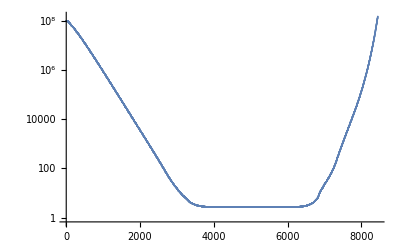

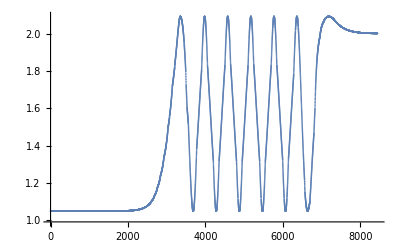

```mathematica
data=Import["C:\\Users\\WalkerXin\\Documents\\Scripts\\tidal_disruption\\integrator_unified\\data\\trace_a_0.50_Q_0.50_lambda_0.50_scale_1.00.dat"];

tlist=Part[data,;;,1];
rlist=Part[data,;;,2];
costhetalist=Part[data,;;,3];
thetalist=ArcCos[costhetalist];
philist=Part[data,;;,4];

dtlist=Part[data,;;,5];
drlist=Part[data,;;,6];
dcosthetalist=Part[data,;;,7];
dthetalist=-dcosthetalist/Sqrt[1-costhetalist^2];
dphilist=Part[data,;;,8];

p1=ListLogPlot[rlist] (*in log scale*)
p2=ListPlot[thetalist,GridLines->{None,{Pi/2}}]
```

Check specific index

```mathematica
Msub=1;
asub=0.5;
Qsub=0.5;
lamsub=0.5;
esub=0;
epsub=1;

sol1=solplus[asub,Qsub,lamsub][[1]];
ibsoplus={r->rsol/. sol1,lz->momentum[rsol/. sol1,asub,Qsub],cart->carterk[rsol/. sol1,asub,Qsub],q->carterq[rsol/. sol1,asub,Qsub]}

qsub=q/.ibsoplus;
lzsub=lz/.ibsoplus;
ksub=cart/.ibsoplus;

index=4900;

rsub=rlist[[index]];
thetasub=thetalist[[index]];

dtsub=dtlist[[index]];
drsub=drlist[[index]];
dthetasub=dthetalist[[index]];
dphisub=dphilist[[index]];

sublist={M->Msub,a->asub,Q->Qsub,e->esub,ep->epsub,q->qsub,lz->lzsub,r->rsub,theta->thetasub,cart->ksub};

Print["r = ",rsub,"\n","theta = ",thetasub,"\n","theta/(Pi/2) = ",thetasub/(Pi/2),"\n","dt = ",dtsub,"\n","dr = ",drsub,"\n","dtheta = ",dthetasub,"\n","dphi = ",dphisub]

vels={dt,dr,dtheta,dphi}/. dsub;
vels=vels/. {M->Msub,a->asub,Q->Qsub,e->esub,ep->epsub,q->qsub,lz->lzsub,r->rsub,theta->thetasub}

{dtsub,drsub,dthetasub,dphisub}=vels;

test=ClocH/. {M->Msub,a->asub,Q->Qsub,e->esub,ep->epsub,q->qsub,lz->lzsub,r->rsub,theta->thetasub,dt->dtsub,dr->drsub,dtheta->dthetasub,dphi->dphisub}
Eigensystem[test]//MatrixForm
Print["trace=",Tr[test]]
```

{r→2.70141826077975,lz→2.8637,cart→8.32067,q→2.73359}

r = 2.70144
theta = 1.08195
theta/(Pi/2) = 0.688791
dt = 2.78964
dr = -5.93766×10^-6
dtheta = 0.0874421
dphi = 0.605306

{3.40238,-0.515477,0,0.503427}

{{-1.11022×10^-16,1.11022×10^-16,0.,5.55112×10^-17},{-4.16334×10^-17,0.263554,0.,0.0811062},{0.,0.,-0.254482,0.},{-5.55112×10^-17,0.0811062,0.,-0.0275659}}

(0.284625 | -0.254482 | -0.0486371 | -1.11022×10^-16
{1.90616×10^-16,-0.96787,0.,-0.25145} | {1.82915×10^-17,0.,-1.,-6.94057×10^-32} | {8.89422×10^-16,-0.25145,0.,0.96787} | {1.,4.08136×10^-16,1.82915×10^-17,-8.12915×10^-16})

trace=-0.0184948

Use Mathematica for complete eigen computation
Mathematica is extremely slow at this (~50 mins per run)
Unless absolutely necessary, use C++ script instead (~1 second per run)

```mathematica
length=5000; (* large enough to cover interesting physics *)
outputtot= ConstantArray[0, {length}];

asub=0.9;
Msub=1;
epsub=1;
qsub=1.9855427062707292;
lzsub=2.4406204372683984;
ksub=qsub+(lzsub-asub*epsub)^2;

Do[outputtot[[i]]=Eigensystem[ClocH/. {a->asub,M->Msub,ep->epsub,q->qsub,lz->lzsub,r->rlist[[i]],theta->thetalist[[i]],
dt->dtlist[[i]],dr->drlist[[i]],dtheta->dthetalist[[i]],dphi->dphilist[[i]]}],
{i,1,length}
]//AbsoluteTiming
```

5000

Part::partw: Part 1 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

```mathematica
Export["tensor_data_final.txt",Re[outputtot],"CSV"]
```

tensor_data_final.txt